```mathematica
SetDirectory["D:\\TimeDepthModels"]
<<WLGPNTeam`TimeDepthModels`
```

D:\TimeDepthModels

### COMBINE TWO GEOLOGICAL TYPES

```mathematica
listH ={100,1}; (*мощности слоев*)
slopes = {0Degree,  0 Degree, 0 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = -1 ;

(*folding parametres *)
hDispersion = 1500;(*степень складчатости нижнего слоя в метрах*)
hTapering =15; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 8; (*start filter radius for GaussianFilter*)


horizonsTop = DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
optsDepthTop = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizonsTop]] - 1)],
						PlotLabel -> "Depth Section"};

PlotDepthSection[horizonsTop, optsDepthTop]

(*второй набор горизонтов*)
listH ={400,500,10, 400, 1000}; (*мощности слоев*)
slopes = {0Degree, 0 Degree, 0 Degree, 0Degree, 0Degree, 0Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = 1 ;

(*folding parametres *)
hDispersion = 500;(*степень складчатости нижнего слоя в метрах*)
hTapering =1; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 3; (*start filter radius for GaussianFilter*)


horizonsBot= DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
optsDepthBot = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizonsBot]] - 1)],
						PlotLabel -> "Глубинный разрез"};

optsDepthResult:={Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizonsResult]] - 1)],
						PlotLabel -> "Глубинный разрез"};

PlotDepthSection[horizonsBot, optsDepthBot]

(*добавили тренд от нижнего горизонта первого набора в во 2ой горизонт второго набора*)
plus = # - Mean[horizonsTop[[-1,All,2]]]&/@horizonsTop[[-1,All,2]]; (*тренд*)
horizonsResult = horizonsBot;
horizonsResult[[2,All,2]]+=plus;   (*2ой т.к. 1ый - нули*)
PlotDepthSection[horizonsResult, optsDepthResult]


(*проверяем если 2ой и 3ий гризонт второго сета пересеклись, добавляем дельту, если нет то ничего *)
t=Table[horizonsResult[[3,j,2]]-horizonsResult[[2,j,2]], {j, Length[horizonsResult[[2]]]}]; 
If[Not[AllTrue[t,#<0&]], For[j=1, j<=Length[horizonsResult[[2]]],j++, horizonsResult[[2,j,2]]+=1.1Max[t]]];(**)
PlotDepthSection[horizonsResult, optsDepthResult]

(*надо удалить самый верхний горизонт. можно было сразу это сдлетаь*)
horizonsResult=Delete[horizonsResult, 1];
horizonsTop=Delete[horizonsTop,1];

(*создаем таблицу значений дельта h для оставшихся выше горизонтов*)
tab = Table[Table[{horizonsTop[[-i-1,j,1]], -horizonsTop[[-i,j,2]]+horizonsTop[[-i-1,j,2]]},{j, Length[horizonsTop[[i]]]}], {i, Length[horizonsTop]-1}];

(*формируем вышележащие горизонты
проверяем что каждый новый горизонт не пересекается с нижележащим
отодвигаем вверх если пересекается на величину пересчения х 1.1*)

For[i=1, i<=Length[tab],i++, z=Table[{tab[[i,j,1]], horizonsResult[[1,j,2]]+tab[[i,j,2]]},{j,Length[horizonsResult[[1]]]}];
horizonsResult=Join[{z}, horizonsResult];
t=Table[horizonsResult[[2,j,2]]-horizonsResult[[1,j,2]], {j, Length[horizonsResult[[1]]]}];
If[Not[AllTrue[t,#<0&]], For[j=1, j<=Length[horizonsResult[[1]]],j++, horizonsResult[[1,j,2]]+=1.1Max[t]]]
];

PlotDepthSection[horizonsResult, optsDepthResult]


(*все горизонты опускаем ниже нуля*)
t=horizonsResult[[1,All,2]];
If[Not[AllTrue[t,#<0&]], 
For[i=1,i<=Length[horizonsResult],i++,
For[j=1, j<=Length[horizonsResult[[i]]],j++, horizonsResult[[i,j,2]]-=1.1Max[t]]
]
]

(*добавляем нулевой горизонт*)
surface = Table[{(j - 1) dx, 0}, {j, len/dx + 1}];
horizonsResult=Join [{surface}, horizonsResult];   
PlotDepthSection[horizonsResult, optsDepthResult]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

CHECK

```mathematica
listH ={100,1}; (*мощности слоев*)
slopes = {0Degree,  0 Degree, 0 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = -1 ;

(*folding parametres *)
hDispersion = 1500;(*степень складчатости нижнего слоя в метрах*)
hTapering =15; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 8; (*start filter radius for GaussianFilter*)


horizonsTop = DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
optsDepthTop = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizonsTop]] - 1)],
						PlotLabel -> "Depth Section"};

PlotDepthSection[horizonsTop, optsDepthTop]

(*второй набор горизонтов*)
listH ={400,500,10, 400, 1000}; (*мощности слоев*)
slopes = {0Degree, 0 Degree, 0 Degree, 0Degree, 0Degree, 0Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = 1 ;

(*folding parametres *)
hDispersion = 500;(*степень складчатости нижнего слоя в метрах*)
hTapering =1; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 3; (*start filter radius for GaussianFilter*)


horizonsBot= DepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
optsDepthBot = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizonsBot]] - 1)],
						PlotLabel -> "Глубинный разрез"};
PlotDepthSection[horizonsBot, optsDepthBot]
```

-Graphics-

-Graphics-

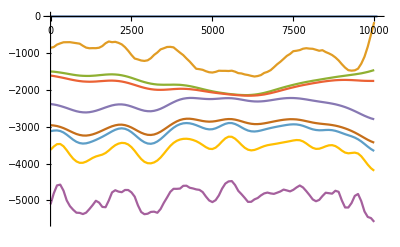

```mathematica
horizonsResult=DepthSection[horizonsTop, horizonsBot][["horizons"]];
PlotDepthSection[horizonsResult]
```

### EXPORT

```mathematica
ExportDepthSection["D:\\TimeDepthModels\\Export\\ds.dat", horizonsResult]
```

D:\TimeDepthModels\Export\ds.dat